## VE401 RC 2

## Continuous Random Variables

#### Exponential Distribution

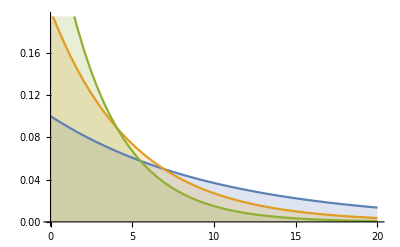

```mathematica
Plot[Table[PDF[ExponentialDistribution[β], x], {β, {0.1, 0.2, 0.3}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Gamma Distribution

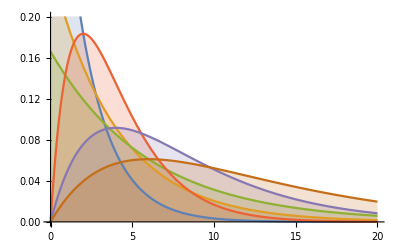

```mathematica
Plot[Table[PDF[GammaDistribution[α, β], x], {α, {1, 2}}, {β, {2, 4, 6}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Chi-Squared Distribution

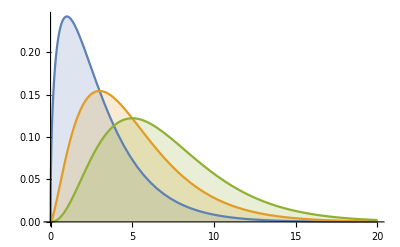

```mathematica
Plot[Table[PDF[ChiSquareDistribution[γ], x], {γ, {3, 5, 7}}] // Evaluate, {x, 0, 20}, Filling->Axis]
```

### Normal Distribution

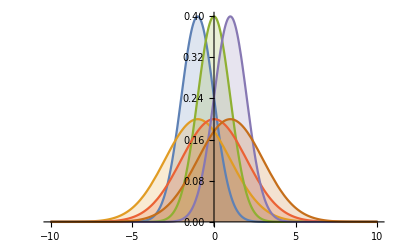

```mathematica
Plot[Table[PDF[NormalDistribution[μ, σ], x], {μ, {-1, 0, 1}}, {σ, {1, 2}}] // Evaluate, {x, -10, 10}, Filling->Axis]
```

## VE401 RC 4

## Statistical Distributions

### Standard Normal Distribution

```mathematica
InverseCDF[NormalDistribution[0, 1], 0.95]
```

1.64485

```mathematica
InverseCDF[NormalDistribution[0, 1], 0.975]
```

1.95996

### Chi-squared Distribution

```mathematica
InverseCDF[ChiSquareDistribution[10], 0.95]
```

18.307

### T Distribution

```mathematica
InverseCDF[StudentTDistribution[10], 0.95]
```

1.81246

## Case Study

```mathematica
X = Round[RandomVariate[NormalDistribution[4.5, 2], 70], 0.01]
n = 70
```

{1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.27,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.85,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.02,6.82,1.24,3.66,0.94,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.63,0.62,3.49,3.06,2.76,5.47,3.26,5.77,6.64,5.74,2.19,1.42,3.82,2.76,2.29,6.93}

```mathematica
X={1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.2700000000000005,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.8500000000000005,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.0200000000000005,6.82,1.24,3.66,0.9400000000000001,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.6300000000000001,0.62,3.49,3.06,2.7600000000000002,5.47,3.2600000000000002,5.7700000000000005,6.640000000000001,5.74,2.19,1.42,3.8200000000000003,2.7600000000000002,2.29,6.93}
```

{1.67,3.6,2.67,11.3,3.86,2.67,4.43,5.86,3.12,2.86,7.24,3.31,4.98,6.68,3.27,6.32,3.94,4.14,4.9,1.98,7.27,5.84,1.33,7.86,4.12,2.39,9.,5.03,6.03,7.85,1.94,3.52,5.49,6.57,8.9,7.73,5.18,4.3,7.37,5.02,6.82,1.24,3.66,0.94,2.22,5.37,3.13,2.44,3.43,3.89,4.53,1.37,4.88,3.15,1.63,0.62,3.49,3.06,2.76,5.47,3.26,5.77,6.64,5.74,2.19,1.42,3.82,2.76,2.29,6.93}

```mathematica
n=Length[X]
```

70

```mathematica
{q1, q2, q3} = Quartiles[X]
iqr = InterquartileRange[X]
h = 2iqr / 70^(1/3)
Min[X]-0.005
Select[X, 1.5+0.615≥ #≥0.615&]
```

{2.76,3.915,5.84}

3.08

1.49468

0.615

{1.67,1.98,1.33,1.94,1.24,0.94,1.37,1.63,0.62,1.42}

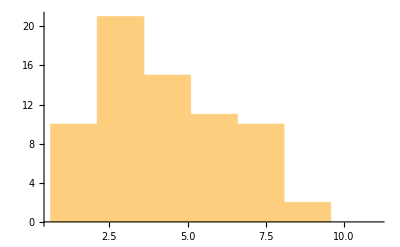

```mathematica
Histogram[X, {Min[X]-0.005, Max[X], h}]
```

```mathematica
Needs["StatisticalPlots`"]
StemLeafPlot[Floor[X, 0.1], IncludeEmptyStems->True]
```

Stem | Leaves
0 | 69
1 | 23346699
2 | 1223466778
3 | 0111223445668889
4 | 11245899
5 | 0013447788
6 | 0356689
7 | 223788
8 | 9
9 | 0
10 | 
11 | 3
Stem units: 1

```mathematica
f1 = q1 - 3/2*iqr
f3 = q3 + 3/2 *iqr
F1 = q1 - 3iqr
F3 = q3 + 3iqr
a1 = Min[Select[X, #≥f1&]]
a3 = Max[Select[X, #≤f3&]]
```

-1.86

10.46

-6.48

15.08

0.62

9.

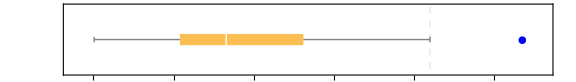

```mathematica
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,0.1]],Max[Ceiling[X,0.1]]],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

```mathematica
Mean[X]
Variance[X]
```

4.378

4.89576

```mathematica
z = InverseCDF[NormalDistribution[0, 1], 0.975]
Mean[X]-2z/Sqrt[70]
Mean[X]+2z/Sqrt[70]
```

1.95996

3.90948

4.84652

```mathematica
c1 = InverseCDF[ChiSquareDistribution[69], 0.025]
c2 = InverseCDF[ChiSquareDistribution[69], 0.975]
(n-1)Variance[X]/c2
(n-1)Variance[X]/c1
```

47.9242

93.8565

3.59919

7.04879

```mathematica
t = InverseCDF[StudentTDistribution[69], 0.975]
Mean[X] - t Variance[X]/Sqrt[n]
Mean[X] + t Variance[X]/Sqrt[n]
```

1.99495

3.21065

5.54535

{188.12,193.71,193.73,195.45,200.81,201.63,202.2,202.21,203.62,204.55,208.15,211.14,219.54,221.31,224.39,226.16}

{198.13,202.915,215.34}

17.21

172.315

241.155

146.5

266.97

188.12

226.16

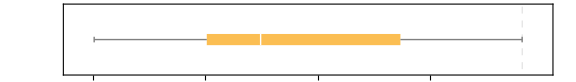

```mathematica
(*** For QA ***)
X = {188.12, 193.71, 193.73, 195.45, 200.81, 201.63, 202.2, 202.21, 203.62, 204.55, 208.15, 211.14, 219.54, 221.31, 224.39, 226.16}
{q1, q2, q3} = Quartiles[X]
iqr = InterquartileRange[X]
f1 = q1 - 3/2*iqr
f3 = q3 + 3/2 *iqr
F1 = q1 - 3iqr
F3 = q3 + 3iqr
a1 = Min[Select[X, #≥f1&]]
a3 = Max[Select[X, #≤f3&]]
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,1]],Max[Ceiling[X,1]], 10],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

```mathematica
(*** Lec 11 ***)
data = {79,141,228,3,20,14,97,194,28,56,75,37,122,27,10,67,23,20,103,11,92,99,64,6,118,136,682,4,70,11,74,40,16,114,8,149,97,7,317,346,188,149,68,150,88,87,155,50,26,143,126,98,153,238,30,53,132,260,296,25,61,87,33,51,74,111,72,178,4,67,43,229,156,117,104,27,23,23,186,524,107,160,41,50,352,8,153,142,306,320,85,44,116,39,264,360,192,142,44,29}
n=Length[data]
```

{79,141,228,3,20,14,97,194,28,56,75,37,122,27,10,67,23,20,103,11,92,99,64,6,118,136,682,4,70,11,74,40,16,114,8,149,97,7,317,346,188,149,68,150,88,87,155,50,26,143,126,98,153,238,30,53,132,260,296,25,61,87,33,51,74,111,72,178,4,67,43,229,156,117,104,27,23,23,186,524,107,160,41,50,352,8,153,142,306,320,85,44,116,39,264,360,192,142,44,29}

100

```mathematica
{q1, q2, q3} = Quartiles[data]
iqr = InterquartileRange[data]
h = 2iqr/n^(1/3)
m1 = Min[data]-0.5
m2 = Max[data]
```

{35,87,299/2}

229/2

229/10^(2/3)

2.5

682

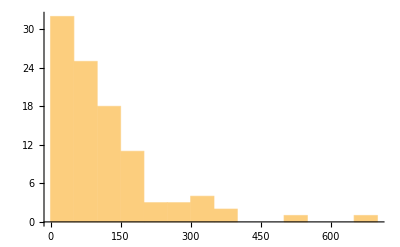

```mathematica
Histogram[data, "FreedmanDiaconis"]
```

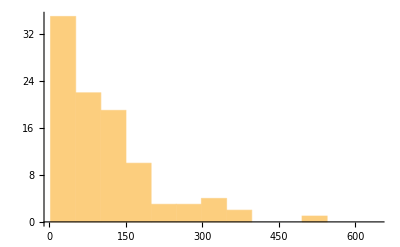

```mathematica
Histogram[data,{m1, m2, h}]
```

{7.78,5.5,6.2,6.08,7.35,6.71,6.19,8.26,8.26,7.47,7.37,4.62,7.96,7.36,7.24,7.05,6.4,4.02,7.72,6.91,6.45,6.52,8.57,5.56,8.71,6.6,6.71,6.64,6.67,7.54,7.66,6.59,7.97,7.61,7.28,7.5,7.55,7.5,7.62,6.87,5.25,5.71,5.99,7.91,7.36,5.75,7.18,7.11,6.8,5.6,6.6,6.46,7.6,7.,7.54,5.6,6.25,8.02,6.59,7.76,7.97,6.22,7.43,6.68,6.69,8.71,7.91,6.86,5.53,7.95}

{6.45,7.025,7.61}

1.16

0.57

4.015

9.145

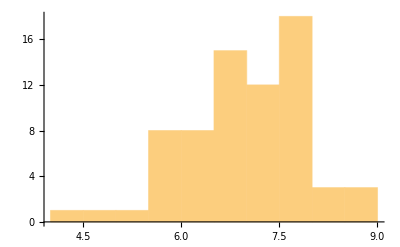

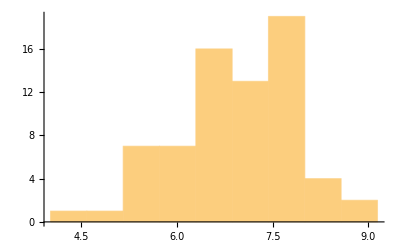

```mathematica
(*** test ***)
n = 70;
precision = 0.01;
data = Round[RandomVariate[NormalDistribution[7, 1], n], precision]
{q1, q2, q3} = Quartiles[data]
iqr = InterquartileRange[data]
h = Ceiling[2iqr/n^(1/3),precision]
l = Min[data]-precision/2
u = Ceiling[(Max[data]-l)/h,1]*h+l
Histogram[data, "FreedmanDiaconis"]
Histogram[data,{l, u, h}]
```

## Assignment 4

### Ex. 4.1

Stem | Leaves | Counts
532 | 9 | 1
533 |  | 0
534 | 2 | 1
535 | 47 | 2
536 | 6 | 1
537 | 5678 | 4
538 | 12345778888 | 11
539 | 016999 | 6
540 | 11166677889 | 11
541 | 123666688 | 9
542 | 0011222357899 | 13
543 | 01111556 | 8
544 | 00012455678 | 11
545 | 233447899 | 9
546 | 23569 | 5
547 | 357 | 3
548 | 11257 | 5
Stem units: 10

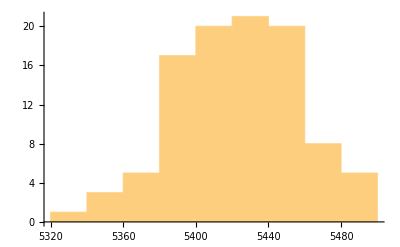

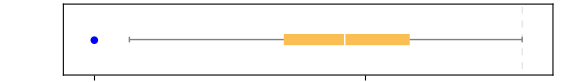

```mathematica
X = {5408,5431,5475,5442,5376,5388,5459,5422,5416,5435,5420,5429,5401,5446,5487,5416,5382,5357,5388,5457,5407,5469,5416,5377,5454,5375,5409,5459,5445,5429,5463,5408,5481,5453,5422,5354,5421,5406,5444,5466,5399,5391,5477,5447,5329,5473,5423,5441,5412,5384,5445,5436,5454,5453,5428,5418,5465,5427,5421,5396,5381,5425,5388,5388,5378,5481,5387,5440,5482,5406,5401,5411,5399,5431,5440,5413,5406,5342,5452,5420,5458,5485,5431,5416,5431,5390,5399,5435,5387,5462,5383,5401,5407,5385,5440,5422,5448,5366,5430,5418};
Needs["StatisticalPlots`"]
StemLeafPlot[X, IncludeEmptyStems->True,IncludeStemCounts->True,StemExponent->{1,"UnitDivisions"->1}]
Histogram[X, "FreedmanDiaconis"]
{q1, q2, q3} = Quartiles[X];
iqr = InterquartileRange[X];
f1 = q1 - 3/2*iqr;
f3 = q3 + 3/2 *iqr;
F1 = q1 - 3iqr;
F3 = q3 + 3iqr;
a1 = Min[Select[X, #≥f1&]];
a3 = Max[Select[X, #≤f3&]];
BoxWhiskerChart[
X, {"Outliers", {"Outliers",Blue},{"FarOutliers",Red}},
AspectRatio->1/7, BarOrigin->Left,
GridLines->{{{a3,Dashed},{F3,Dashed}},None},ImageSize->Large,FrameTicks->{
{None,None},
{Range[Min[Floor[X,1]],Max[Ceiling[X,1]], 100],
{{q1,"q1"},{q2,"q2"},{q3,"q3"},{a3,"near"},{F3,"far"}}}}
]
```

## VE401 RC 5

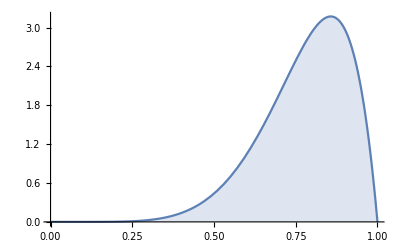

```mathematica
Plot[PDF[BetaDistribution[7, 2], x], {x, 0, 1}, Filling->Axis]
```

```mathematica
p=CDF[BetaDistribution[7,2],0.5]
(1-p)/p
```

0.0351563

27.4444

```mathematica
data={41.50,41.38,42.24,41.85,41.76,42.08,41.62,42.16,41.71,41.44};
Needs["HypothesisTesting`"]
FisherRatioTest[data,0.1,"TestDataTable",AlternativeHypothesis->"Unequal"]
```

| Statistic | P-Value
Fisher Ratio | 8.3544 | 0.997726

```mathematica
1-CDF[ChiSquareDistribution[19],29.503]
```

0.0584741

```mathematica
data = {5,1,5,4,4,6,6,3,6,2,3,5,5,6,4,4,4,3,3,4};
m0=3;
Qp=Length[Select[data, #>m0&]] (* Q+ *)
Qm=Length[Select[data, #<m0&]] (* Q- *)
n=Qp+Qm;
SignTest[data,m0,"TestDataTable",AlternativeHypothesis->"Greater"]
CDF[BinomialDistribution[n,0.5],Qp]
CDF[BinomialDistribution[n,0.5],Qm]
```

14

2

| Statistic | P-Value
Sign | 14 | 0.00209045

0.999741

0.00209045

```mathematica
data={1,2,3,3,3,3,4,4,4,4,4,4,5,5,5,5,6,6,6,6};
m0=3.5;
SignedRankTest[data,m0,"TestDataTable",AlternativeHypothesis->"Greater"]
```

| Statistic | P-Value
Signed-Rank | 157. | 0.0251201

## Exercise 1.

```mathematica
n=12;
data=Round[RandomVariate[NormalDistribution[2.7, 1], n],0.01]
```

{1.85,3.53,3.22,3.11,3.78,2.81,4.16,3.32,4.01,2.5,4.,2.95}

```mathematica
n1=16;
X1={2.55,2.11,2.76,2.19,2.94,2.41,2.27,1.98,2.72,2.26,2.65,2.68,2.15,2.33,2.32,1.88};
n2=12;
X2={2.85,2.73,2.92,2.11,1.78,2.01,2.16,2.32,2.51,2.53,2.67,2.75};
(* mean *)
t1=InverseCDF[StudentTDistribution[n1-1],0.975]
T1=(Mean[X1]-2.30)/(StandardDeviation[X1]/Sqrt[n1])
Mean[X1]-t1*StandardDeviation[X1]/Sqrt[n1]
Mean[X1]+t1*StandardDeviation[X1]/Sqrt[n1]
0.2/StandardDeviation[X1]
(* variance *)
c1=InverseCDF[ChiSquareDistribution[n1-1],0.05]
C1=(n1-1)StandardDeviation[X1]^2/0.5^2
(n1-1)StandardDeviation[X1]^2/c1^2
StandardDeviation[X1]/0.5
(* sign test *)
m0=2.5;
qp=Length[Select[X1,#>m0&]]
qm=Length[Select[X1,#<m0&]]
SignTest[X1,m0,"TestDataTable",AlternativeHypothesis->"Unequal"]
CDF[BinomialDistribution[n1,0.5],qp]
CDF[BinomialDistribution[n1,0.5],qm]
(* signed rank test *)
m0=2.5;
order=Ordering[Abs[X1-m0]];
X1[[order]]
Sort[Abs[X1-m0]]
1+3+5+7+10+14
-2-4-6-8-9-11-12-13-15-16
mean=N[n1(n1+1)/4]
stddev=N[Sqrt[n1(n1+1)(2n1+1)/24]]
InverseCDF[NormalDistribution[0,1],0.975]
(96-mean)/stddev
(* test proportion *)
p0=0.5;
p1=Length[Select[X1,2.3+0.4># &&2.3-0.4<#&]]/n1
(p1-p0)/Sqrt[p0(1-p0)/n1]
InverseCDF[NormalDistribution[0,1],0.95]
(* compare proportions *)
p2=N[Length[Select[X2,2.3+0.4># &&2.3-0.4<#&]]/n2]
p=N[(n1*p1+n2*p2)/(n1+n2)]
(p1-p2)/Sqrt[p(1-p)(1/n1+1/n2)]
InverseCDF[NormalDistribution[0,1],0.975]
(* compare variances *)
s1=StandardDeviation[X1]
s2=StandardDeviation[X2]
s1^2
s2^2
f1=(s1/s2)^2
f2=(s2/s1)^2
InverseCDF[FRatioDistribution[n1-1,n2-1],0.975]
InverseCDF[FRatioDistribution[n2-1,n1-1],0.975]
```

2.13145

1.15816

2.22647

2.54853

0.661807

7.26094

5.4796

0.0259838

0.604406

6

10

| Statistic | P-Value
Sign | 6 | 0.454498

0.227249

0.894943

{2.55,2.41,2.65,2.33,2.68,2.32,2.72,2.27,2.26,2.76,2.19,2.15,2.11,2.94,1.98,1.88}

{0.05,0.09,0.15,0.17,0.18,0.18,0.22,0.23,0.24,0.26,0.31,0.35,0.39,0.44,0.52,0.62}

40

-96

68.

19.3391

1.95996

1.44785

3/4

2.

1.64485

0.583333

0.678571

0.934502

1.95996

0.302203

0.365128

0.0913267

0.133318

0.685028

1.45979

3.32993

3.00783

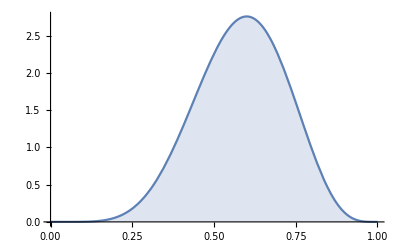

```mathematica
Plot[PDF[BetaDistribution[7, 5], x], {x, 0, 1}, Filling->Axis]
```

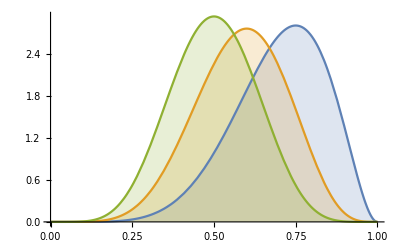

```mathematica
Plot[Table[PDF[BetaDistribution[7,b], x], {b, {3, 5, 7}}] // Evaluate, {x, 0, 1}, Filling->Axis]
```

## VE401 RC6

## Exercise 1.

```mathematica
n=20;
X1=Round[RandomVariate[NormalDistribution[2.7, 1], n],0.01]
X2=Round[RandomVariate[NormalDistribution[2.5, 1], n],0.01]
```

{3.73,2.9,2.58,3.33,3.34,2.8,3.84,3.01,2.91,0.83,4.54,3.49,1.12,0.78,0.67,2.32,2.42,3.21,3.09,1.16}

{1.3,2.55,3.03,1.71,2.45,1.58,2.68,1.07,2.45,2.72,2.54,2.59,2.35,2.42,2.87,4.13,1.73,2.42,3.03,1.23}

```mathematica
n=20;
X1={3.73,2.9,2.58,3.33,3.34,2.8,3.84,3.01,2.91,0.83,4.54,3.49,1.12,0.78,0.67,2.32,2.42,3.21,3.09,1.16};
X2={1.3,2.55,3.03,1.71,2.45,1.58,2.68,1.07,2.45,2.72,2.54,2.59,2.35,2.42,2.87,4.13,1.73,2.42,3.03,1.23};
```

```mathematica
m1=Mean[X1]
m2=Mean[X2]
```

2.6035

2.3425

```mathematica
(m1-m2)/Sqrt[1/10]
```

0.825354

```mathematica
InverseCDF[NormalDistribution[0,1],0.975]
```

1.95996

```mathematica
var1=Variance[X1]
var2=Variance[X2]
varp=(var1+var2)/2
```

1.26328

0.53442

0.898848

```mathematica
(m1-m2)/Sqrt[2varp/n]
```

0.870557

```mathematica
InverseCDF[StudentTDistribution[38],0.975]
```

2.02439

```mathematica
0.5/(2Sqrt[varp])
```

0.263692

```mathematica
(var1/n+var2/n)^2/((var1/n)^2/(n-1)+(var2/n)^2/(n-1))
```

32.6354

```mathematica
(m1-m2)/Sqrt[var1/n+var2/n]
```

0.870557

```mathematica
InverseCDF[StudentTDistribution[32],0.975]
```

2.03693

## Exercise 2.

```mathematica
p=N[(42+72+15+4)/(12*100)]
```

0.110833

```mathematica
p1=Binomial[12,0]*(1-p)^(12)
p2=Binomial[12,1]*p(1-p)^(11)
p3=Binomial[12,2]*p^2(1-p)^(10)
p4=Binomial[12,3]*p^3(1-p)^(9)
p5=1-Binomial[12,0]*(1-p)^(12)-Binomial[12,1]*p(1-p)^(11)-Binomial[12,2]*p^2(1-p)^(10)-Binomial[12,3]*p^3(1-p)^(9)
```

0.244229

0.365314

0.250447

0.10406

0.0359493

```mathematica
p5*100
```

3.59493

```mathematica
n=100;
(16-n*p1)^2/(n*p1)+(42-n*p2)^2/(n*p2)+(36-n*p3)^2/(n*p3)+(5-n*p4)^2/(n*p4)+(1-n*p5)^2/(n*p5)
```

13.1972

```mathematica
InverseCDF[ChiSquareDistribution[3],0.95]
```

7.81473